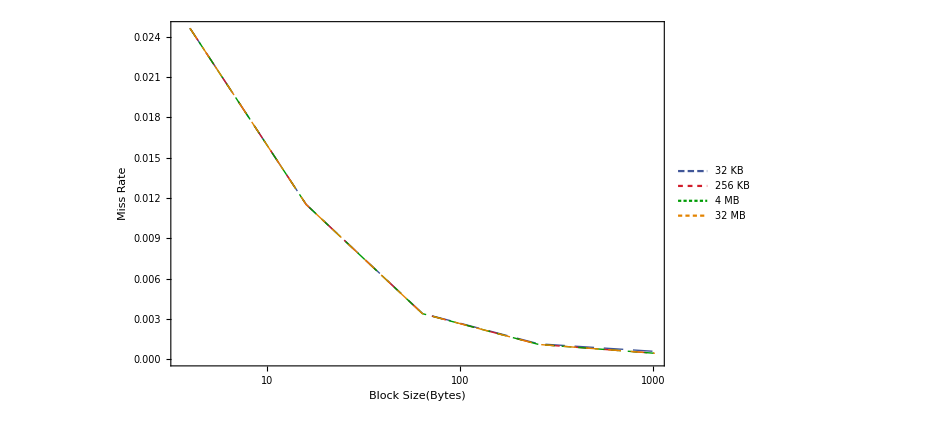

```mathematica
(*block32klist={{4,0.011580},{16,0.005645},{64,0.001645},{256,0.000554},{1024,0.000257}};
block256klist={{4,0.011559},{16,0.005628},{64,0.001609},{256,0.000499},{1024,0.000187}};
block4mlist={{4,0.011559},{16,0.005628},{64,0.001609},{256,0.000499},{1024,0.000187}};
block32mlist={{4,0.011559},{16,0.005628},{64,0.001609},{256,0.000499},{1024,0.000187}};*)

block32klist={{4,0.024620},{16,0.011513},{64,0.003417},{256,0.001149},{1024,0.000586}};
block256klist={{4,0.024620},{16,0.011508},{64,0.003395},{256,0.001103},{1024,0.000445}};
block4mlist={{4,0.024620},{16,0.011508},{64,0.003395},{256,0.001103},{1024,0.000445}};
block32mlist={{4,0.024620},{16,0.011508},{64,0.003395},{256,0.001103},{1024,0.000445}};

frame[legend_]:=Framed[legend,FrameStyle->{Black,Thin},RoundingRadius->5,Background->White];
ListLogLinearPlot[{block32klist,block256klist,block4mlist,block32mlist},PlotRange->{Full,Full},Joined->True,Frame->True,FrameTicks->{{All,None},{{4,16,64,256,1024},None}},GridLines->{{4,16,64,256,1024}, None},GridLinesStyle->{{LightGray,Thin},{LightGray,Thick}},
FrameStyle->Thickness[Medium],FrameTicksStyle->{{Directive[Black,FontFamily->"Helvetica",13],None},{Directive[Black,FontFamily->"Helvetica",13],None}},PlotStyle->{{RGBColor[64/255,86/255,152/255],Dashing[{0.02,0.01}],Thin},{RGBColor[209/255,29/255,43/255],Dashing[{0.015,0.015}],Thin},{RGBColor[0/255,156/255,4/255],Dashing[{0.01,0.007}],Thin},{RGBColor[227/255,131/255,0/255],Dashing[{0.013,0.01}],Thin},{RGBColor[121/255,17/255,152/255],Dashing[{0.01,0.01}],Thin}},PlotLegends->Placed[LineLegend[{"32 KB","256 KB","4 MB","32 MB"},LegendFunction->frame,LabelStyle->{13,FontFamily->"Helvetica"},LegendMarkerSize->{{50,4}}],{0.63,0.76}],
FrameLabel->{Style["Block Size(Bytes)",FontFamily->"Helvetica",Black,15],Style["Miss Rate",FontFamily->"Helvetica",Black,15]}]
```